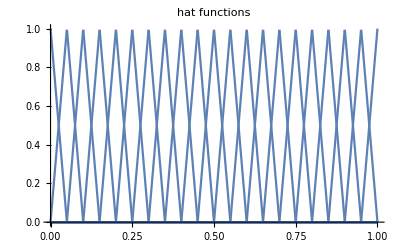

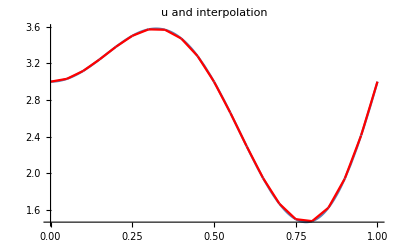

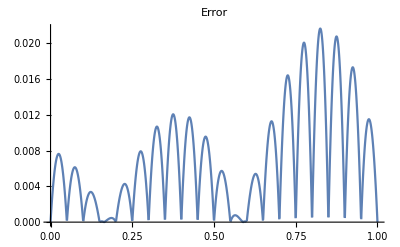

0.00874337

0.439738

```mathematica
hat[i_,points_, x_]:=
Which[
i≥2&&i≤Length[points]-1,
Piecewise[{
{(x-points[[i-1]])/(points[[i]]-points[[i-1]]),Between[x,{points[[i-1]],points[[i]]}]},
{(points[[i+1]]-x)/(points[[i+1]]-points[[i]]),Between[x,{points[[i]],points[[i+1]]}]}
},0],
i==1,
Piecewise[{
{(points[[i+1]]-x)/(points[[i+1]]-points[[i]]),Between[x,{points[[i]],points[[i+1]]}]}
},0],
i==Length[points],
Piecewise[{
{(x-points[[i-1]])/(points[[i]]-points[[i-1]]),Between[x,{points[[i-1]],points[[i]]}]}
},0]
]

n=20;
points = Table[k/n,{k,0,n}];

Show[Table[Plot[hat[i, points, x],{x,First[points],Last[points]}, PlotRange->All,PlotLegends->"Expressions"],{i,1,n+1}], PlotLabel-> "hat functions"]

u[x_]:=2 x Sin[2 Pi x]+3
hatInterpolate[u_,points_, x_]:=Sum[u[points[[i]]]hat[i, points, x],{i,1,Length[points]}]
interpolationError[u_,points_,x_]:=u[x]-hatInterpolate[u, points, x]

maxStep[points_]:=Max[Table[points[[i+1]]-points[[i]],{i,1,Length[points]-1}]]

L2Norm[u_,a_,b_]:=Sqrt[NIntegrate[u[x]^2,{x,a,b}]]
aprioriErrorEstimate[u_,points_]:= Sqrt[Length[points]] L2Norm[u'',First[points],Last[points]] maxStep[points]^2  
errorNorm[u_,points_]:=Sqrt[NIntegrate[interpolationError[u,points,x]^2,{x,First[points],Last[points]}]]

Show[
{Plot[u[x],{x,First[points],Last[points]}, PlotRange->All]},{Plot[hatInterpolate[u, points, x],{x,First[points],Last[points]}, PlotRange->All,PlotStyle->Red]},PlotLabel->"u and interpolation"
]


Plot[Abs[interpolationError[u,points,x]],{x,First[points],Last[points]}, PlotLabel->"Error"]


errorNorm[u,points]
aprioriErrorEstimate[u,points]
```